# 1) Explicit SK parameter tendency equations

## Define the SK explicit tendency equations for the near field KRoNUT (precomputed

Here (ẇ)_(*n), (L̇)_n, and (Ḣ)_n depend on w_(*n), L_n, and H_nas well as the choice of ν.

Note that the equations have been split such that the self advection terms and dissipation terms are separated. On the RHS of the equation the self-advection term appear first followed by the dissipation term.

### w_n(w_(*n),L_n,H_n) tendency {(ẇ)_(*n)}

```mathematica
DwnSKwLH[ν_,wn_,Ln_,Hn_]=-(ⅇ (64 Hn^4-32 Hn^2 Ln^2-Ln^4) wn^2)/(128 Hn^3 (8 Hn^2+3 Ln^2))-(ν (256 Hn^6+160 Hn^4 Ln^2-16 Hn^2 Ln^4-Ln^6) wn)/(4 Hn^4 Ln^2 (8 Hn^2+3 Ln^2));
```

### L_n(w_(*n),L_n,H_n) tendency {(L̇)_n}

```mathematica
DLnSKwLH[ν_,wn_,Ln_,Hn_]=-(5 ⅇ Ln^3 wn)/(256 Hn^3+96 Hn Ln^2)+(ν (16 Hn^4+18 Hn^2 Ln^2+Ln^4))/(8 Hn^4 Ln+3 Hn^2 Ln^3);
```

### H_n(w_(*n),L_n,H_n) tendency {(Ḣ)_(*n)}

```mathematica
DHnSKwLH[ν_,wn_,Ln_,Hn_]=(ⅇ (64 Hn^4+Ln^4) wn)/(128 Hn^2 (8 Hn^2+3 Ln^2))+(ν (32 Hn^4-4 Hn^2 Ln^2+Ln^4))/(32 Hn^5+12 Hn^3 Ln^2);
```

## Preform a substitution on the SK explicit tendency (dot) equations

Here  w_(*n), L_n, and H_nas well as ν are re-expressed in (ẇ)_(*n), (L̇)_n, and (Ḣ)_nvia w_(*n),α_n, R_n and τ_nwhere:

Geometric aspect ratio: α_n=L_n/H_n

Turbulent Reynolds number:  R_n=(w_(*n×H_n))/ν

Characteristic turnover time: τ_n=H_n/(w_(*n)).

α_n and R_nare dimensionless quantities while τ_ncarries the dimensions of time of time.

(ẇ)_(*n)is the only term which carries a dependence on w_(*n),α_n, R_n and τ_n, (L̇)_(*n) and (Ḣ)_(*n)carry no τ_n dependence but still depend on w_(*n),α_n, R_n.

### w_(n*)(w_(*n),α_n,R_n,τ_n) tendency { (ẇ)_(*n)}

```mathematica
DwnSK[wn_,τn_,αn_,Rn_]=Collect[DwnSKwLH[(ⅇ*wn*wn*τn)/Rn,wn,wn*τn*αn,wn*τn],Rn,Simplify];
```

### L_n(w_(*n),α_n,R_n) tendency {(L̇)_(*n)}

```mathematica
DLnSK[wn_,αn_,Rn_]=Collect[DLnSKwLH[(ⅇ*wn*Hn)/Rn,wn,Hn*αn,Hn],Rn,Simplify];
```

### H_n(w_(*n),α_n,R_n) tendency {(Ḣ)_(*n)}

```mathematica
DHnSK[wn_,αn_,Rn_]=Collect[DHnSKwLH[(ⅇ*wn*Hn)/Rn,wn,Hn*αn,Hn],Rn,Simplify];
```

## 2) Null surfaces for the explicit SK parameters and their Intersection

## Solve for the explicit parameter null surfaces

While we solve for the explicit null surfaces, we do this with respect to the implicit parameters thus null surfaces live in the implicit parameter phase space.

This is done by solving for R_n under the condition that the tendency equation under consideration is equal to zero {ex. (ẇ)_(*n)=0}

There is no null surface associated with (Ḣ)_(*n) as this tendency equation is positive definite

### w_(*n) null surface

```mathematica
Solve[DwnSK[wn,τn,αn,Rn]==0,Rn]
```

{{Rn→-(32 (-256-160 αn^2+16 αn^4+αn^6))/(αn^2 (-64+32 αn^2+αn^4))}}

### L_(*n) null surface

```mathematica
Solve[DLnSK[wn,αn,Rn]==0,Rn]
```

{{Rn→(32 (16+18 αn^2+αn^4))/(5 αn^4)}}

## Set the explicit parameter null surfaces

### w_(*n) null surface

```mathematica
wnαRNullcline[αn_]=-(32 (-256-160 αn^2+16 αn^4+αn^6))/(αn^2 (-64+32 αn^2+αn^4));
```

### L_n null surface

```mathematica
LnαRNullcline[αn_]=(32 (16+18 αn^2+αn^4))/(5 αn^4);
```

## Solve for the intersection of the w_(*n) and L_n null surfaces

This is done to find the point in the α_n-R_n subspace where the w_(*n) and L_n null surfaces intersect.

To do this we equate the null surfaces, solve for the associated α_n, and plug that α_n into one of the null surface equations

These quantities are relevant because they appear in because the corresponding point in the α_n-R_nspace corresponds to a constant integrated mass flux, (σ̇)_n=0

This point however is not a fixed point in the phase space and thus (σ̇)_n=0 is not a preferred state of thecloudy circulations

### Equate the the null surfaces and solve for α_n

```mathematica
N[Solve[wnαRNullcline[αn]==LnαRNullcline[αn],αn,Assumptions->αn>0]];
```

### Set the α_nvalue associated with the intersection

```mathematica
αnExplicitFixed=SetPrecision[2.154834495516665,3]
```

2.15

### Plug the α_n value into the L_n null surface equation and set the R_nvalue associated with the intersection

```mathematica
RnExplicitFixed=SetPrecision[LnαRNullcline[2.154834495516665],3]
```

36.

## 3) Implicit SK parameter tendency equations

## Solve for the SK implicit tendency equations for the near field KRoNUT (precomputed

Here (α̇)_n, (Ṙ)_n, and (τ̇)_n depend on w_(*n), L_n, and H_nas well as the choice of ν.

### α_n(w_(*n),L_n,H_n) tendency {(α̇)_n}

```mathematica
DαnSKwLH[ν_,wn_,Ln_,Hn_]=Simplify[(DLnSKwLH[ν,wn,Ln,Hn]*Hn-Ln*DHnSKwLH[ν,wn,Ln,Hn])/Hn^2];
```

### R_n(w_(*n),L_n,H_n) tendency {(Ṙ)_(*n)}

```mathematica
DRnSKwLH[ν_,wn_,Ln_,Hn_]=Simplify[ⅇ*(DHnSKwLH[ν,wn,Ln,Hn]*wn+Hn*DwnSKwLH[ν,wn,Ln,Hn])/ν];
```

### τ_n(w_(*n),L_n,H_n) tendency {(τ̇)_n}

```mathematica
DτnSKwLH[ν_,wn_,Ln_,Hn_]=Simplify[(DHnSKwLH[ν,wn,Ln,Hn]*wn-Hn*DwnSKwLH[ν,wn,Ln,Hn])/wn^2];
```

## Preform a substitution on the SK implicit tendency (dot) equations

Unlike the explicit parameter tendency equations, which had w_(*n) dependence in each term, there is no w_(*n)dependence in the implicit parameter tendency equations.

(α̇)_n and (Ṙ)_n depend on all of the implicit parameters while τ_n only depends on α_n and R_n.

### α_n(α_n,R_n,τ_n) tendency {(α̇)_n}

```mathematica
DαnSK[τn_,αn_,Rn_]=Collect[DαnSKwLH[(ⅇ*wn*τn*wn)/Rn,wn,wn*τn*αn,wn*τn],Rn,Simplify];
```

### R_n(α_n,R_n,τ_n) tendency {(Ṙ)_n}

```mathematica
DRnSK[τn_,αn_,Rn_]=Collect[DRnSKwLH[(ⅇ*wn*τn*wn)/Rn,wn,wn*τn*αn,wn*τn],Rn,Simplify];
```

### τ_n(α_n,R_n) tendency {(τ̇)_n}

```mathematica
DτnSK[αn_,Rn_]=Collect[DτnSKwLH[(ⅇ*wn*τn*wn)/Rn,wn,wn*τn*αn,wn*τn],Rn,Simplify];
```

## 4) SK Implicit null surface analysis

## Solve for SK implicit null surfaces

Here the implicit parameter null surfaces are solved by setting the implicit tendency equation, which are functions of the implicit parameters, equal to zero and solving for the R_n ((α̇)_n=0->R_n= ...).

Here the implicit null surfaces are functions of the implicit parameters and thus the surfaces live in the implicit parameter phase plane.

### α_n null surface

```mathematica
Solve[DαnSK[τn,αn,Rn]==0,Rn];
```

### R_n null surface

```mathematica
Solve[DRnSK[τn,αn,Rn]==0,Rn];
```

### τ_n null surface

```mathematica
Solve[DτnSK[αn,Rn]==0,Rn];
```

## Set SK implicit null surfaces

Computed in the above subsection.

### αn null surface

```mathematica
RnNullSurfaceSK[αn_]=-(32 (-128-64 αn^2+6 αn^4+αn^6))/(αn^4 (16+αn^2));
```

### Rn null surface

```mathematica
αnNullSurfaceSK[αn_]=-(32 (-64-40 αn^2-8 αn^4+αn^6))/(αn^2 (64+20 αn^2+αn^4));
```

### τn null surface

```mathematica
τnNullSurfaceSK[αn_]=-(4 (-64-48 αn^2+5 αn^4))/(αn^2 (-4+αn^2));
```

## Find the line along which the α_n and R_n null surfaces intersect

Given the positive definite nature of the implicit parameters only one of these points makes physical sense, (α_n,R_n)=(2 √(1/3 (1+√7)),8/27 (-5+17 √7))

### Solve for αn associated with αn_* and Rn null surfaces intersect

```mathematica
Solve[DαnSK[τn,αn,RnNullSurfaceSK[αn]]==0,αn];
```

### Plug in the αn_* value into the Rn null surface equation to compute Rn_*

```mathematica
Simplify[RnNullSurfaceSK[2 √(1/3 (1+√7))]];
```

## Define the (α_n,R_n) associated with the fixed line, (α_n^*, R_n^*)

#### Exact

```mathematica
FixedLineSK={2 √(1/3 (1+√7)),8/27 (-5+17 √7)};
```

#### Numeric

```mathematica
FixedLineSKN=N[FixedLineSK]
```

{2.20477,11.8453}

## 5) SK Fixed Line Analysis

## Define the Jacobian

```mathematica
JSK[τn_,αn_,Rn_]=Simplify[{{D[DαnSK[τn,αn,Rn],αn],D[DαnSK[τn,αn,Rn],Rn]},{D[DRnSK[τn,αn,Rn],αn],D[DRnSK[τn,αn,Rn],Rn]}}];
```

## Compute the trace, the determinant, and the discriminant of the Jacobian evaluated at the fixed line

These values still depend on τ_nbut give the positive definite nature of τ_nand the fact that it can be scaled out of each term, τ_n has no appreciable role in determining the sign of the trace, determinant, or discriminant which is what we care able for a linear stability analysis.

#### Trace

```mathematica
TraceSK[τn_]=Simplify[JSK[τn,FixedLineSK[[1]],FixedLineSK[[2]]][[1]][[1]]+JSK[τn,FixedLineSK[[1]],FixedLineSK[[2]]][[2]][[2]]];
```

#### Determinant

```mathematica
DeterminantSK[τn_]=Simplify[JSK[τn,FixedLineSK[[1]],FixedLineSK[[2]]][[1]][[1]]*JSK[τn,FixedLineSK[[1]],FixedLineSK[[2]]][[2]][[2]]-JSK[τn,FixedLineSK[[1]],FixedLineSK[[2]]][[1]][[2]]*JSK[τn,FixedLineSK[[1]],FixedLineSK[[2]]][[2]][[1]]];
```

#### Discriminant

```mathematica
DiscriminantSK[τn_]=Simplify[TraceSK[τn]^2-4*DeterminantSK[τn]];
```

## Stability analysis of fixed line

Given that τ_ncannot affect the underlying sign of the of the trace, determinant, and discriminant we set it equal to 1.

### Numeric (τn == 1)

#### Trace

```mathematica
N[DiscriminantSK[1]];
```

#### Determinant

```mathematica
N[DeterminantSK[1]];
```

#### Discriminant

```mathematica
N[TraceSK[1]];
```

## Compute (τ̇)_n along the fixed line

Here we determine the behavior of τ_nas KRoNUT trajectories asymptote to the fixed line/preferred circulation.

#### Exact

```mathematica
Simplify[DτnSK[FixedLineSK[[1]],FixedLineSK[[2]]]];
```

#### Numeric

```mathematica
N[Simplify[DτnSK[FixedLineSK[[1]],FixedLineSK[[2]]]]];
```

# 6) SK circulation

## SK circulation tendency equations (Precomputed

Here Γ̇ depend on w_(*n), L_n, and H_nas well as the choice of ν.

### Γ_n(w_n,L_n,H_n) tendency {Γ̇}

```mathematica
DΓnSK[ν_,wn_,Ln_,Hn_]=Simplify[(ⅇ (-8 Hn^2-(32 Hn^4)/Ln^2+3 Ln^2) wn ν)/(4 Hn^3)];
```

## Preform a substitution on the SK circulation tendency equation

Here Γ̇ depends on w_n, α_n, R_n

### Γ_n(α_n,R_n,H_n) tendency {Γ̇}

```mathematica
DΓnαR[wn_,αn_,τn_]=Collect[DΓnSK[(ⅇ*wn*τn*wn)/Rn,wn,wn*τn*αn,wn*τn],Rn,Simplify]
```

(ⅇ^2 wn^2 (-32-8 αn^2+3 αn^4))/(4 Rn αn^2)

## Compute Γ_n along the fixed line

Here Γ_nalong the fixed line corresponds to the fixed circulation, Γ_n^* which in the case of the

### Define Γn (precomputed

```mathematica
ΓnSK[ν_,αn_,Rn_]=ν*Rn*(αn^2/4+1);
```

#### Exact

```mathematica
Simplify[ΓnSK[ν,FixedLineSK[[1]],FixedLineSK[[2]]]];
```

#### Numeric

```mathematica
N[Simplify[ΓnSK[ν,FixedLineSK[[1]],FixedLineSK[[2]]]]];
```

# 7) SK integrated mass flux

## Define the integrated mass flux of the near field KRoNUT, σ_n (precomputed

```mathematica
σSK[wn_,Ln_]=(π*Ln^2*wn)/ⅇ;
```

## Compute the general tendency equation for σ_n

The purpose of this computation is to show that given the positive definite nature of L_n and w_(*n)the only for σ_n=0 is if (L̇)_n and (ẇ)_(*n) are both equal to zero, i.e the L_n and  w_(*n), null surfaces.

The point in the α_n-R_n subspace of the implicit parameter phase space corresponding to the intersection of the  L_n and w_n null surfaces was computed in section 2 of this document.

By general tendency equation we mean that we haven’t plugged in the precomputed (L̇)_n and (ẇ)_n.

```mathematica
DσSK=Simplify[D[σSK[wn[t],Ln[t]],t]];
```

## Plug the (α_n, R_n) values associated with the intersection of the L_n and w_(*n), null surfaces into (α̇)_n(α_n,R_n,τ_n) and (Ṙ)_n(α_n,R_n,τ_n)

The purpose of this calculation is to demonstrate that (α̇)_n≠0 and (Ṙ)_n≠0 at the intersection point thus there is no steady state integrated mass flux

### α_n(2.15, 36.0, τ_n)

```mathematica
DαnSK[τn,αnExplicitFixed,RnExplicitFixed];
```

### R_n(2.15, 36.0, τ_n)

```mathematica
DRnSK[τn,αnExplicitFixed,RnExplicitFixed];
```

## 8) Explicit DK parameter tendency equations

Here (ẇ)_(*n), (L̇)_n, (Ḣ)_n, (ẋ)_nand (ẏ)_n depend on w_(*n), L_n, H_n ,x_n, y_n,  w_(*f), L_f, H_f, x_f,and y_fas well as the choice of ν.

## Define the DK explicit tendency equations for the near field KRoNUT (precomputed

### w_n(w_(*n),L_n,H_n,x_n,y_n,w_(*f),L_f,H_f,x_f,y_f) tendency {(ẇ)_(*n)}

```mathematica
DwnDDwLH[ν_,wn_,Ln_,Hn_,xn_,yn_,wf_,Lf_,Hf_,xf_,yf_]=Collect[-((8 ⅇ π Hn wn ((2 ⅇ π Ln^3 wn (32 ν Hn^3 wn+8 ν Hn Ln^2 wn-(3 ν Ln^4 wn)/Hn))/Hn+(ⅇ π Ln^7 wn^2 (24 ν-ⅇ Hn wn+(8 ⅇ^(-(-Lf^2+(xf-xn)^2+(yf-yn)^2)/Lf^2) Hf Hn^2 (Hf+3 Hn) wf (-Lf^2+(xf-xn)^2+(yf-yn)^2))/((Hf+Hn)^3 Lf^2)))/(8 Hn^2))-((ⅇ π Ln^7 wn^2)/Hn+(2 ⅇ π Ln^3 wn (4 Hn^2 Ln^2 wn-Ln^4 wn))/Hn) (-(ⅇ π ν (-32 Hn^4+Ln^4) wn)/(Hn^2 Ln^2)-(ⅇ^2 π (8 Hn^2+Ln^2) wn^2)/(32 Hn)-(ⅇ^(2-((xf-xn)^2+(yf-yn)^2)/Lf^2) π Hf Hn (4 Hf Hn+Ln^2) wf wn (Lf^2-(xf-xn)^2-(yf-yn)^2))/((Hf+Hn)^3 Lf^2)))/(32 ⅇ^2 π^2 Hn^3 Ln^5 wn^2+12 ⅇ^2 π^2 Hn Ln^7 wn^2)),ν,Simplify];
```

### L_n(w_(*n),L_n,H_n,x_n,y_n,w_(*f),L_f,H_f,x_f,y_f) tendency {(L̇)_n}

```mathematica
DLnDDwLH[ν_,wn_,Ln_,Hn_,xn_,yn_,wf_,Lf_,Hf_,xf_,yf_]=Collect[-((ⅇ^(-(xf-xn)^2/Lf^2-(yf-yn)^2/Lf^2) (-512 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf^3 Hn^4 Lf^2-1536 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf^2 Hn^5 Lf^2-1536 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf Hn^6 Lf^2-512 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hn^7 Lf^2-576 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf^3 Hn^2 Lf^2 Ln^2-1728 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf^2 Hn^3 Lf^2 Ln^2-1728 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf Hn^4 Lf^2 Ln^2-576 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hn^5 Lf^2 Ln^2-32 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf^3 Lf^2 Ln^4-96 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf^2 Hn Lf^2 Ln^4-96 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf Hn^2 Lf^2 Ln^4-32 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hn^3 Lf^2 Ln^4-64 ⅇ Hf^2 Hn^4 Lf^2 Ln^2 wf+192 ⅇ Hf Hn^5 Lf^2 Ln^2 wf+48 ⅇ Hf^2 Hn^2 Lf^2 Ln^4 wf+112 ⅇ Hf Hn^3 Lf^2 Ln^4 wf+5 ⅇ^(1+(xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) Hf^3 Hn Lf^2 Ln^4 wn+15 ⅇ^(1+(xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) Hf^2 Hn^2 Lf^2 Ln^4 wn+15 ⅇ^(1+(xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) Hf Hn^3 Lf^2 Ln^4 wn+5 ⅇ^(1+(xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) Hn^4 Lf^2 Ln^4 wn+64 ⅇ Hf^2 Hn^4 Ln^2 wf xf^2-192 ⅇ Hf Hn^5 Ln^2 wf xf^2-48 ⅇ Hf^2 Hn^2 Ln^4 wf xf^2-112 ⅇ Hf Hn^3 Ln^4 wf xf^2-128 ⅇ Hf^2 Hn^4 Ln^2 wf xf xn+384 ⅇ Hf Hn^5 Ln^2 wf xf xn+96 ⅇ Hf^2 Hn^2 Ln^4 wf xf xn+224 ⅇ Hf Hn^3 Ln^4 wf xf xn+64 ⅇ Hf^2 Hn^4 Ln^2 wf xn^2-192 ⅇ Hf Hn^5 Ln^2 wf xn^2-48 ⅇ Hf^2 Hn^2 Ln^4 wf xn^2-112 ⅇ Hf Hn^3 Ln^4 wf xn^2+64 ⅇ Hf^2 Hn^4 Ln^2 wf yf^2-192 ⅇ Hf Hn^5 Ln^2 wf yf^2-48 ⅇ Hf^2 Hn^2 Ln^4 wf yf^2-112 ⅇ Hf Hn^3 Ln^4 wf yf^2-128 ⅇ Hf^2 Hn^4 Ln^2 wf yf yn+384 ⅇ Hf Hn^5 Ln^2 wf yf yn+96 ⅇ Hf^2 Hn^2 Ln^4 wf yf yn+224 ⅇ Hf Hn^3 Ln^4 wf yf yn+64 ⅇ Hf^2 Hn^4 Ln^2 wf yn^2-192 ⅇ Hf Hn^5 Ln^2 wf yn^2-48 ⅇ Hf^2 Hn^2 Ln^4 wf yn^2-112 ⅇ Hf Hn^3 Ln^4 wf yn^2))/(32 Hn^2 (Hf+Hn)^3 Lf^2 Ln (8 Hn^2+3 Ln^2))),ν,Simplify];
```

### H_n(w_(*n),L_n,H_n,x_n,y_n,w_(*f),L_f,H_f,x_f,y_f) tendency {(Ḣ)_(*n)}

```mathematica
DHnDDwLH[ν_,wn_,Ln_,Hn_,xn_,yn_,wf_,Lf_,Hf_,xf_,yf_]=Collect[-((ⅇ^(-(xf-xn)^2/Lf^2-(yf-yn)^2/Lf^2) (-1024 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf^3 Hn^4 Lf^2-3072 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf^2 Hn^5 Lf^2-3072 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf Hn^6 Lf^2-1024 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hn^7 Lf^2+128 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf^3 Hn^2 Lf^2 Ln^2+384 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf^2 Hn^3 Lf^2 Ln^2+384 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf Hn^4 Lf^2 Ln^2+128 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hn^5 Lf^2 Ln^2-32 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf^3 Lf^2 Ln^4-96 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf^2 Hn Lf^2 Ln^4-96 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hf Hn^2 Lf^2 Ln^4-32 ⅇ^((xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) ν Hn^3 Lf^2 Ln^4-1024 ⅇ Hf^2 Hn^6 Lf^2 wf+128 ⅇ Hf Hn^5 Lf^2 Ln^2 wf-32 ⅇ Hf Hn^3 Lf^2 Ln^4 wf-64 ⅇ^(1+(xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) Hf^3 Hn^5 Lf^2 wn-192 ⅇ^(1+(xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) Hf^2 Hn^6 Lf^2 wn-192 ⅇ^(1+(xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) Hf Hn^7 Lf^2 wn-64 ⅇ^(1+(xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) Hn^8 Lf^2 wn-ⅇ^(1+(xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) Hf^3 Hn Lf^2 Ln^4 wn-3 ⅇ^(1+(xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) Hf^2 Hn^2 Lf^2 Ln^4 wn-3 ⅇ^(1+(xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) Hf Hn^3 Lf^2 Ln^4 wn-ⅇ^(1+(xf-xn)^2/Lf^2+(yf-yn)^2/Lf^2) Hn^4 Lf^2 Ln^4 wn+1024 ⅇ Hf^2 Hn^6 wf xf^2-128 ⅇ Hf Hn^5 Ln^2 wf xf^2+32 ⅇ Hf Hn^3 Ln^4 wf xf^2-2048 ⅇ Hf^2 Hn^6 wf xf xn+256 ⅇ Hf Hn^5 Ln^2 wf xf xn-64 ⅇ Hf Hn^3 Ln^4 wf xf xn+1024 ⅇ Hf^2 Hn^6 wf xn^2-128 ⅇ Hf Hn^5 Ln^2 wf xn^2+32 ⅇ Hf Hn^3 Ln^4 wf xn^2+1024 ⅇ Hf^2 Hn^6 wf yf^2-128 ⅇ Hf Hn^5 Ln^2 wf yf^2+32 ⅇ Hf Hn^3 Ln^4 wf yf^2-2048 ⅇ Hf^2 Hn^6 wf yf yn+256 ⅇ Hf Hn^5 Ln^2 wf yf yn-64 ⅇ Hf Hn^3 Ln^4 wf yf yn+1024 ⅇ Hf^2 Hn^6 wf yn^2-128 ⅇ Hf Hn^5 Ln^2 wf yn^2+32 ⅇ Hf Hn^3 Ln^4 wf yn^2))/(128 Hn^3 (Hf+Hn)^3 Lf^2 (8 Hn^2+3 Ln^2))),ν,Simplify];
```

### x_n(w_(*n),L_n,H_n,x_n,y_n,w_(*f),L_f,H_f,x_f,y_f) tendency {(ẋ)_n}

```mathematica
DxnDDwLH[ν_,wn_,Ln_,Hn_,xn_,yn_,wf_,Lf_,Hf_,xf_,yf_]=FullSimplify[-1/(8 (Hf+Hn)^3 Lf^4 (4 Hn^2+Ln^2))ⅇ^(-(xf-xn)^2/Lf^2-(yf-yn)^2/Lf^2) (-8 ⅇ Hf^2 Hn^2 Lf^4 wf xf+8 ⅇ Hf Hn^3 Lf^4 wf xf-2 ⅇ Hf^2 Lf^4 Ln^2 wf xf-6 ⅇ Hf Hn Lf^4 Ln^2 wf xf+6 ⅇ Hf^2 Lf^2 Ln^4 wf xf+18 ⅇ Hf Hn Lf^2 Ln^4 wf xf-3 ⅇ Hf^2 Ln^4 wf xf^3-9 ⅇ Hf Hn Ln^4 wf xf^3+8 ⅇ Hf^2 Hn^2 Lf^4 wf xn-8 ⅇ Hf Hn^3 Lf^4 wf xn+2 ⅇ Hf^2 Lf^4 Ln^2 wf xn+6 ⅇ Hf Hn Lf^4 Ln^2 wf xn-6 ⅇ Hf^2 Lf^2 Ln^4 wf xn-18 ⅇ Hf Hn Lf^2 Ln^4 wf xn+9 ⅇ Hf^2 Ln^4 wf xf^2 xn+27 ⅇ Hf Hn Ln^4 wf xf^2 xn-9 ⅇ Hf^2 Ln^4 wf xf xn^2-27 ⅇ Hf Hn Ln^4 wf xf xn^2+3 ⅇ Hf^2 Ln^4 wf xn^3+9 ⅇ Hf Hn Ln^4 wf xn^3-3 ⅇ Hf^2 Ln^4 wf xf yf^2-9 ⅇ Hf Hn Ln^4 wf xf yf^2+3 ⅇ Hf^2 Ln^4 wf xn yf^2+9 ⅇ Hf Hn Ln^4 wf xn yf^2+6 ⅇ Hf^2 Ln^4 wf xf yf yn+18 ⅇ Hf Hn Ln^4 wf xf yf yn-6 ⅇ Hf^2 Ln^4 wf xn yf yn-18 ⅇ Hf Hn Ln^4 wf xn yf yn-3 ⅇ Hf^2 Ln^4 wf xf yn^2-9 ⅇ Hf Hn Ln^4 wf xf yn^2+3 ⅇ Hf^2 Ln^4 wf xn yn^2+9 ⅇ Hf Hn Ln^4 wf xn yn^2)];
```

### y_n(w_(*n),L_n,H_n,x_n,y_n,w_(*f),L_f,H_f,x_f,y_f) tendency {(ẏ)_n}

```mathematica
DynDDwLH[ν_,wn_,Ln_,Hn_,xn_,yn_,wf_,Lf_,Hf_,xf_,yf_]=FullSimplify[-1/(8 (Hf+Hn)^3 Lf^4 (4 Hn^2+Ln^2))ⅇ^(-(xf-xn)^2/Lf^2-(yf-yn)^2/Lf^2) (-8 ⅇ Hf^2 Hn^2 Lf^4 wf yf+8 ⅇ Hf Hn^3 Lf^4 wf yf-2 ⅇ Hf^2 Lf^4 Ln^2 wf yf-6 ⅇ Hf Hn Lf^4 Ln^2 wf yf+6 ⅇ Hf^2 Lf^2 Ln^4 wf yf+18 ⅇ Hf Hn Lf^2 Ln^4 wf yf-3 ⅇ Hf^2 Ln^4 wf xf^2 yf-9 ⅇ Hf Hn Ln^4 wf xf^2 yf+6 ⅇ Hf^2 Ln^4 wf xf xn yf+18 ⅇ Hf Hn Ln^4 wf xf xn yf-3 ⅇ Hf^2 Ln^4 wf xn^2 yf-9 ⅇ Hf Hn Ln^4 wf xn^2 yf-3 ⅇ Hf^2 Ln^4 wf yf^3-9 ⅇ Hf Hn Ln^4 wf yf^3+8 ⅇ Hf^2 Hn^2 Lf^4 wf yn-8 ⅇ Hf Hn^3 Lf^4 wf yn+2 ⅇ Hf^2 Lf^4 Ln^2 wf yn+6 ⅇ Hf Hn Lf^4 Ln^2 wf yn-6 ⅇ Hf^2 Lf^2 Ln^4 wf yn-18 ⅇ Hf Hn Lf^2 Ln^4 wf yn+3 ⅇ Hf^2 Ln^4 wf xf^2 yn+9 ⅇ Hf Hn Ln^4 wf xf^2 yn-6 ⅇ Hf^2 Ln^4 wf xf xn yn-18 ⅇ Hf Hn Ln^4 wf xf xn yn+3 ⅇ Hf^2 Ln^4 wf xn^2 yn+9 ⅇ Hf Hn Ln^4 wf xn^2 yn+9 ⅇ Hf^2 Ln^4 wf yf^2 yn+27 ⅇ Hf Hn Ln^4 wf yf^2 yn-9 ⅇ Hf^2 Ln^4 wf yf yn^2-27 ⅇ Hf Hn Ln^4 wf yf yn^2+3 ⅇ Hf^2 Ln^4 wf yn^3+9 ⅇ Hf Hn Ln^4 wf yn^3)];
```

## Reorganize the explicit DK tendency equations that depend on the explicit parameters

Here, the terms on the right hand side of the equation go self-advection, cross-advection, and the dissipation effects

```mathematica
FullSimplify[DwnDDwLH[ν,wn,Ln,Hn,xn,yn,wf,Lf,Hf,xf,yf]-DwnSKwLH[ν,wn,Ln,Hn]]+DwnSKwLH[ν,wn,Ln,Hn];
```

```mathematica
FullSimplify[DLnDDwLH[ν,wn,Ln,Hn,xn,yn,wf,Lf,Hf,xf,yf]-DLnSKwLH[ν,wn,Ln,Hn]]+DLnSKwLH[ν,wn,Ln,Hn];
```

```mathematica
FullSimplify[DHnDDwLH[ν,wn,Ln,Hn,xn,yn,wf,Lf,Hf,xf,yf]-DHnSKwLH[ν,wn,Ln,Hn]]+DHnSKwLH[ν,wn,Ln,Hn];
```

## Preform a substitution on the DK explicit tendency equations

Here  w_(*n), L_n, and H_nas well as ν are re-expressed in (ẇ)_(*n), (L̇)_n, and (Ḣ)_nvia w_(*n),H_n,α_n, R_n where:

Geometric aspect ratio: α_n=L_n/H_n

Turbulent Reynolds number:  R_n=(w_(*n×H_n))/ν

Characteristic turnover time: τ_n=H_n/(w_(*n))

Distance between convective core centers: d=((x_f-x_n)^2+(y_f-y_n)^2)^(1/2)

angle of separation as measured from the near field: ϕ_nf=(y_f-y_n)/(x_f-x_n)

Cross interaction distance scaled: Λ_f=d/L_f

Updraft radii ratio: Υ_nf=L_n/L_f

Height of maximum vertical velocity ratio: Π_nf=H_n/H_f

Although not not used in the substitution, it is apparent that τ_n appears in (ẇ)_n.

Here, the tendency equations are not separated into self-advection, cross-advection, and dissipation terms.

α_n, R_n, Λ_f, Υ_nf, Π_nf,ϕ_nf are dimensionless quantities.

### w_n(w_(*n),H_n, α_n, R_n, w_f,Λ_nf,Π_nf) tendency {(ẇ)_(*n)}

```mathematica
DwnDDαR[wn_,Hn_,αn_,Rn_, Π_,Λ_,wf_]=Collect[Simplify[DwnDDwLH[(ⅇ*wn*Hn)/Rn,wn,Hn*αn,Hn,xf-d*Cos[θd],yf-d*Sin[θd],wf,d/Λ,Hn/Π,xf,yf]],Rn];
```

### L_n(w_(*n), α_n, R_n, w_f,Λ_nf,Π_nf) tendency {(L̇)_(*n)}

```mathematica
DLnDDαR[wn_,αn_,Rn_, Π_,Λ_,wf_]=Collect[Simplify[DLnDDwLH[(ⅇ*wn*Hn)/Rn,wn,Hn*αn,Hn,xf-d*Cos[θd],yf-d*Sin[θd],wf,d/Λ,Hn/Π,xf,yf]],Rn];
```

### H_n(w_(*n), α_n, R_n, w_f,Λ_nf,Π_nf) tendency {(Ḣ)_(*n)}

```mathematica
DHnDDαR[wn_,αn_,Rn_, Π_,Λ_,wf_]=Collect[Simplify[DHnDDwLH[(ⅇ*wn*Hn)/Rn,wn,Hn*αn,Hn,xf-d*Cos[ϕnf],yf-d*Sin[ϕnf],wf,d/Λ,Hn/Π,xf,yf]],Rn ];
```

### x_n(w_(*n), α_n, R_n, w_(*f), Λ_nf, Π_nf, Υ_nf, ϕ_nf) tendency {(ẋ)_n}

```mathematica
DxnDDαR[wn_,αn_,Rn_, Π_,Λ_,wf_,Υ_,ϕnf_]=Collect[DxnDDwLH[(ⅇ*Hn*wn)/Rn,wn,Hn*αn,Hn,xf-(Λ*Hn*αn)/Υ*Cos[ϕnf],yf-(Λ*Hn*αn)/Υ*Sin[ϕnf],wf,(αn*Hn)/Υ,Hn/Π,xf,yf],Υ,FullSimplify];
```

### y_n(w_(*n), α_n, R_n, w_(*f), Λ_nf, Π_nf, Υ_nf, ϕ_nf) tendency {(ẏ)_n}

```mathematica
DxnDDαR[wn_,αn_,Rn_, Π_,Λ_,wf_,Υ_,ϕnf_]=Collect[DxnDDwLH[(ⅇ*Hn*wn)/Rn,wn,Hn*αn,Hn,xf-(Λ*Hn*αn)/Υ*Cos[ϕnf],yf-(Λ*Hn*αn)/Υ*Sin[ϕnf],wf,(αn*Hn)/Υ,Hn/Π,xf,yf],Υ,FullSimplify];
```

## Isolate the DK term associated with cross-interaction

Note that (ẋ)_n and (ẏ)_nare not included here because they are due entirely to cross-interactions and thus due not need to be isolated.

```mathematica
wnDDsub[αn_,τn_, Π_,Λ_,wf_]=Simplify[DwnDDαR[wn,wn*τn,αn,Rn, Π,Λ,wf]-DwnSK[wn,τn,αn,Rn]];
```

```mathematica
LnDDsub[αn_, Π_,Λ_,wf_]=Simplify[DLnDDαR[wn,αn,Rn, Π,Λ,wf]-DLnSK[wn,αn,Rn]];
```

```mathematica
HnDDsub[αn_, Π_,Λ_,wf_]=Simplify[DHnDDαR[wn,αn,Rn, Π,Λ,wf]-DHnSK[wn,αn,Rn]];
```

## Reorganize the explicit DK tendency equations that depend on the implicit parameters

Here the terms on the right hand side of the equation go self-advection, dissipation effects, and cross-advection.

Note that while the self-interaction and dissipation terms scale with w_(*n)the cross interaction terms scale with w_(*f).

```mathematica
wnDD[wn_,αn_,Rn_,τn_, Π_,Λ_,wf_] =wnDDsub[αn,τn, Π,Λ,wf]+DwnSK[wn,τn,αn,Rn]
```

(ⅇ wn (-64+32 αn^2+αn^4))/(128 (8+3 αn^2) τn)+(ⅇ wn (-256-160 αn^2+16 αn^4+αn^6))/(4 Rn αn^2 (8+3 αn^2) τn)-(ⅇ^(1-Λ^2) wf (-1+Λ^2) Π (-32+αn^4 Π+4 αn^2 (3+4 Π)))/(4 (8+3 αn^2) (1+Π)^3 τn)

```mathematica
LnDD[wn_,αn_,Rn_ Π_,Λ_,wf_]=LnDDsub[αn, Π,Λ,wf]+DLnSK[wn,αn,Rn]
```

-(5 ⅇ wn αn^3)/(256+96 αn^2)+(ⅇ wn (16+18 αn^2+αn^4))/(Rn αn (8+3 αn^2))+(ⅇ^(1-Λ^2) wf αn (-1+Λ^2) Π (-4+12 Π+αn^2 (3+7 Π)))/(2 (8+3 αn^2) (1+Π)^3)

```mathematica
HnDD[wn_,αn_,Rn_, Π_,Λ_,wf_]=HnDDsub[αn, Π,Λ,wf]+DHnSK[wn,αn,Rn]
```

(ⅇ wn (64+αn^4))/(128 (8+3 αn^2))+(ⅇ wn (32-4 αn^2+αn^4))/(4 Rn (8+3 αn^2))-(ⅇ^(1-Λ^2) wf (-1+Λ^2) Π (32-4 αn^2 Π+αn^4 Π))/(4 (8+3 αn^2) (1+Π)^3)

# 9) DK implicit parameter tendency equations

## Define the DK implicit tendency equations for the near field KRoNUT (precomputed

Here (α̇)_n, (Ṙ)_n, and (τ̇)_n depend on w_(*n), L_n, H_n, x_n, y_n, w_(*f), L_f, H_f, x_f,and y_fas well as the choice of ν.

```mathematica
DαnDKwLH[ν_,wn_,Ln_,Hn_,xn_,yn_,wf_,Lf_,Hf_,xf_,yf_]=Simplify[(DLnDDwLH[ν,wn,Ln,Hn,xn,yn,wf,Lf,Hf,xf,yf]*Hn-Ln*DHnDDwLH[ν,wn,Ln,Hn,xn,yn,wf,Lf,Hf,xf,yf])/Hn^2];
```

```mathematica
DRnDKwLH[ν_,wn_,Ln_,Hn_,xn_,yn_,wf_,Lf_,Hf_,xf_,yf_]=Collect[Simplify[ⅇ*(DHnDDwLH[ν,wn,Ln,Hn,xn,yn,wf,Lf,Hf,xf,yf]*wn+Hn*DwnDDwLH[ν,wn,Ln,Hn,xn,yn,wf,Lf,Hf,xf,yf])/ν],wf];
```

```mathematica
DτnDKwLH[ν_,wn_,Ln_,Hn_,xn_,yn_,wf_,Lf_,Hf_,xf_,yf_]=Simplify[(DHnDDwLH[ν,wn,Ln,Hn,xn,yn,wf,Lf,Hf,xf,yf]*wn-Hn*DwnDDwLH[ν,wn,Ln,Hn,xn,yn,wf,Lf,Hf,xf,yf])/wn^2];
```

## Isolate the DK term associated with cross-interaction

```mathematica
DαnDKwLHsub[wf_,Lf_,Hf_,xf_,yf_,Ln_,Hn_,xn_,yn_]=Simplify[DαnDKwLH[ν,wn,Ln,Hn,xn,yn,wf,Lf,Hf,xf,yf]-DαnSKwLH[ν,wn,Ln,Hn]];
```

```mathematica
DRnDKwLHsub[ν_,wf_,Lf_,Hf_,xf_,yf_,Ln_,Hn_,xn_,yn_]=FullSimplify[DRnDKwLH[ν,wn,Ln,Hn,xn,yn,wf,Lf,Hf,xf,yf]-DRnSKwLH[ν,wn,Ln,Hn]];
```

```mathematica
DτnDKwLHsub[wf_,Lf_,Hf_,xf_,yf_,Ln_,Hn_,xn_,yn_]=Simplify[DτnDKwLH[ν,wn,Ln,Hn,xn,yn,wf,Lf,Hf,xf,yf]-DτnSKwLH[ν,wn,Ln,Hn]];
```

## Preform a substitution on the DK implicit tendency equations on the cross-interaction term

```mathematica
DαnDKsub[τf_,αn_,Λ_,Π_]=Simplify[DαnDKwLHsub[wf,d/Λ,wf*τf,xf,yf,αn*Π*wf*τf,Π*wf*τf,xf-d*Cos[ϕnf],yf-d*Sin[ϕnf]]];
```

```mathematica
DRnDKsub[τf_,αn_,Λ_,Π_,Rn_]=Simplify[DRnDKwLHsub[(ⅇ*wn*τf*wf*Π)/Rn, wf,d/Λ,wf*τf,xf,yf,αn*Π*wf*τf,Π*wf*τf,xf-d*Cos[ϕnf],yf-d*Sin[ϕnf]]];
```

```mathematica
DτnDKsub[αn_,Λ_,Π_,Ξ_]=Simplify[DτnDKwLHsub[wn/Ξ,d/Λ,wf*τf,xf,yf,αn*Π*wf*τf,Π*wf*τf,xf-d*Cos[ϕnf],yf-d*Sin[ϕnf]]];
```

## Reorganize the DK implicit tendency equations

Here the terms on the right hand side of the equation go cross-advection, self-advection, and dissipation.

Note that the self-advection and dissipation terms scale with τ_n while the cross advection terms scale with τ_f.

```mathematica
DαnDK[αn_,Rn_,τn_,τf_,Λ_,Π_]=DαnDKsub[τf,αn,Λ,Π]+DαnSK[τn,αn,Rn];
```

```mathematica
DRnDK[αn_,Rn_,τn_,τf_,Λ_,Π_]=DRnDKsub[τf,αn,Λ,Π,Rn]+DRnSK[τn,αn,Rn];
```

```mathematica
DτnDK[αn_,Rn_,Λ_,Π_,Τ_]=DτnDKsub[αn,Λ,Π,Ξ]+DτnSK[αn,Rn];
```

## 10) DK Implicit null surface analysis

## Solve for DK implicit null surfaces

Here the implicit parameter null surfaces are solved by setting the implicit tendency equation, which are functions of the implicit parameters, equal to zero and solving for the R_n ((α̇)_n=0->R_n= ...).

Here the implicit null surfaces are functions of the implicit parameters and thus the surfaces live in the implicit parameter phase plane.

We have introduced an additional non-dimensional implicit parameter here

Maximum vertical velocity ratio: Ξ_nf=(w_(*n))/(w_(*f))

### αn null surface

```mathematica
Simplify[Solve[DαnDK[αn,Rn,(Hf*Π)/(wf*Ξ),Hf/wf,Λ,Π]==0,Rn]];
```

### Rn null surface

```mathematica
Simplify[Solve[DRnDK[αn,Rn,(Hf*Π)/(wf*Ξ),Hf/wf,Λ,Π]==0,Rn]];
```

### τn null surface

```mathematica
Simplify[Solve[DτnDK[αn,Rn,Λ,Π,Ξ]==0,Rn]];
```

## Set DK implicit null surfaces

Computed in the above subsection.

### αn null surface

```mathematica
αnNullSurfaceDK[αn_,Λ_,Π_,Ξ_]=-(32 ⅇ^(Λ^2) (-64-40 αn^2-8 αn^4+αn^6) Ξ (1+Π)^3)/(αn^2 (4+αn^2) (ⅇ^(Λ^2) (16+αn^2) Ξ (1+Π)^3-32 (-1+Λ^2) Π (6+(6+αn^2) Π)));
```

### Rn null surface

```mathematica
RnNullSurfaceDK[αn_,Λ_,Π_,Ξ_]=-(32 ⅇ^(Λ^2) (-128-64 αn^2+6 αn^4+αn^6) Ξ (1+Π)^3)/(αn^4 (ⅇ^(Λ^2) (16+αn^2) Ξ (1+Π)^3-32 (-1+Λ^2) Π (6+(6+αn^2) Π)));
```

### τn null surface

```mathematica
τnNullSurfaceDK[αn_,Λ_,Π_,Ξ_]=-(4 ⅇ^(Λ^2) (-64-48 αn^2+5 αn^4) Ξ (1+Π)^3)/(αn^2 (ⅇ^(Λ^2) (-4+αn^2) Ξ (1+Π)^3-4 (-1+Λ^2) Π (-16+αn^2 (3+5 Π))));
```

# DK fixed line analysis

## Find the line along which the αn and Rn null surfaces intersect

Note that only one of these points makes physical sense, αn=2 √(1/3 (1+√7)).

This corresponds to the same α_n found in the SK fixed line analysis. The same cannot be said for the R_n value which does not directly match its SK values.

### Solve for αn associated with αn_* and Rn null surfaces intersect

```mathematica
Solve[DαnDK[αn,RnNullSurfaceDK[αn,Λ,Π,Ξ],(Hf*Π)/(wf*Ξ),Hf/wf,Λ,Π]==0,αn];
```

### Plug in the αn_* value into the Rn null surface equation to compute Rn_*

```mathematica
Simplify[RnNullSurfaceDK[2 √(1/3 (1+√7)),Λ,Π,(Hf*Π)/(wf*Ξ),Hf/wf]];
```

## Define the fixed line (α_n^*, R_n^*)

```mathematica
FixedLineDK[Λ_,Π_,Ξ_]=Simplify[{2 √(1/3 (1+√7)),(16 (32+17 √7) ⅇ^(Λ^2) Ξ (1+Π)^3)/((4+√7) ((13+√7) ⅇ^(Λ^2) Ξ (1+Π)^3-16 (-1+Λ^2) Π (9+(11+2 √7) Π)))}];
```

## Determine the various limits associated with the R_n^*

### Case 1

```mathematica
Limit[FixedLineDK[Λ,Π,Ξ][[2]],Λ->∞];
```

### Case 2

```mathematica
Limit[FixedLineDK[Λ,Π,Ξ][[2]],Λ->0];
```

### Case 3

```mathematica
Simplify[Limit[FixedLineDK[Λ,Π,Ξ][[2]],Π->∞]];
```

### Case 4

```mathematica
Simplify[Limit[FixedLineDK[Λ,Π,Ξ][[2]],Π->0]];
```

### Case 5

```mathematica
Simplify[Limit[FixedLineDK[Λ,Π,Ξ][[2]],Ξ->∞]];
```

### Case 6

```mathematica
Simplify[Limit[FixedLineDK[Λ,Π,Ξ][[2]],Ξ->0]];
```

## Determine the various limits associated with the Γ_n^*

### Case 1

```mathematica
Limit[ΓnSK[ν,FixedLineDK[Λ,Π,Ξ][[1]],FixedLineDK[Λ,Π,Ξ][[2]]],Λ->∞]
```

(16 (32+17 √7) ν)/(3 (13+√7))

### Case 2

```mathematica
Limit[ΓnSK[ν,FixedLineDK[Λ,Π,Ξ][[1]],FixedLineDK[Λ,Π,Ξ][[2]]],Λ->0];
```

### Case 3

```mathematica
Simplify[Limit[ΓnSK[ν,FixedLineDK[Λ,Π,Ξ][[1]],FixedLineDK[Λ,Π,Ξ][[2]]],Π->∞]];
```

### Case 4

```mathematica
Simplify[Limit[ΓnSK[ν,FixedLineDK[Λ,Π,Ξ][[1]],FixedLineDK[Λ,Π,Ξ][[2]]],Π->0]];
```

### Case 5

```mathematica
Simplify[Limit[ΓnSK[ν,FixedLineDK[Λ,Π,Ξ][[1]],FixedLineDK[Λ,Π,Ξ][[2]]],Ξ->∞]];
```

### Case 6

```mathematica
Simplify[Limit[ΓnSK[ν,FixedLineDK[Λ,Π,Ξ][[1]],FixedLineDK[Λ,Π,Ξ][[2]]],Ξ->0]];
```

# Beth Graphs

```mathematica
ℶΛPlot=Plot[ⅇ^(-Λ^2) (-1+Λ^2),{Λ,0,3},AxesLabel->{"Λ_nf","ℶ(Λ)"},GridLines->Automatic,PlotRange->{-1.01,.21},PlotLabel->"(a) Λ_nfDependence of the Coupling Coefficient",LabelStyle->Bold ];
```

```mathematica
ℶΠPlot=Plot[Π/(Π+1)^3,{Π,0,3},AxesLabel->{"Π_nf","ℶ(Π)"},GridLines->Automatic,PlotRange->{0,.201},PlotStyle->Red,PlotLabel->"(b) Π_nfDependence of the Coupling Coefficient",LabelStyle->Bold ];
```

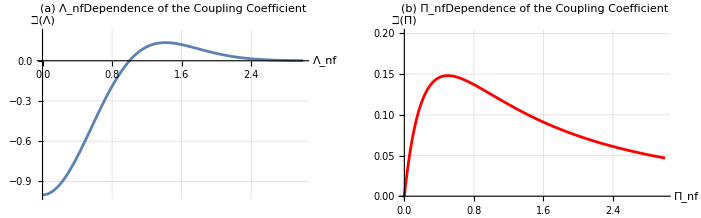

```mathematica
GraphicsGrid[{{ℶΛPlot,ℶΠPlot}},Frame->All]
```